Let’s use Mathematica’s free-form linguistic input to request the US state abbreviations

WolframAlphaQueryParseResults

{AL,AK,AZ,AR,CA,CO,CT,DE,DC,FL,GA,HI,ID,IL,IN,IA,KS,KY,LA,ME,MD,MA,MI,MN,MS,MO,MT,NE,NV,NH,NJ,NM,NY,NC,ND,OH,OK,OR,PA,RI,SC,SD,TN,TX,UT,VT,VA,WA,WV,WI,WY}

Let’s assign that dataset to the variable ‘states’

```mathematica
states=%;
```

Let’s set the base url for PredictIt’s API against which we’ll concatenate each state’s abbreviation to get the latest market prices for which party is predicted to win the White House

Let’s define a variable for the base API url and name format of the Electoral College Contracts

```mathematica
predictitAPIURLBase="http://www.predictit.org/api/marketdata/ticker/";
electoralCollegeContracts="x.USPREZ16";
```

Here we import the latest price data for each of the states and specifically select the Last Trade Price on the contracts

```mathematica
currentPrices={};For[i=1,i≤Length[states],i++,AppendTo[currentPrices,Import[predictitAPIURLBase<>StringReplace[electoralCollegeContracts,"x"->states⟦i⟧],"JSON"]];
Pause[1];
];
partyToWin=Import[predictitAPIURLBase<>"PREZPRTY16","JSON"];
timeStamp=Now;
lastTradePrices={};
For[i=1,i≤Length[currentPrices],i++,
AppendTo[lastTradePrices,{"TickerSymbol","LastTradePrice"}/.("Contracts"/.currentPrices⟦i⟧)]
];
```

Convert the state abbreviations to a Mathematica object that can be passed into the geo plot functions

```mathematica
stateObjects=Interpreter["USState"][#]&/@states;
```

Create a list of mapping rules, assigning each state with its respective GOP price

```mathematica
gopByState=#⟦1⟧->#⟦2⟧&/@Join[{stateObjects,Flatten[Select[#,StringMatchQ[#⟦1⟧,"GOP*"]&]&/@lastTradePrices,1]⟦All,2⟧}ᵀ];
```

Let’s try to calculate the expected electoral vote breakdown applying the PredictIt data. We’ll set a threshold level for winning a state.
First, let’s import the electoral vote breakdown from Wikipedia.

```mathematica
electoralCollegeVotes=Import["http://www.archives.gov/federal-register/electoral-college/allocation.html","Data"];
mappedStateVotes=Interpreter["USState"][#⟦1⟧]->#⟦2⟧&/@electoralCollegeVotes⟦2,1,2;;-1⟧;
```

For each state, let’s determine what camp they are predicted to fall into. We’ll let a threshold (let’s use 60%) where a state is considered allocated. We’ll combine that with the electoral votes to get a count for each candidate and undecided.

```mathematica
cutoffPercentage=0.6;
gopVotes=Total[Select[gopByState,#⟦2⟧≥cutoffPercentage&]⟦All,1⟧/.mappedStateVotes];
demVotes=Total[Select[gopByState,#⟦2⟧≤1-cutoffPercentage&]⟦All,1⟧/.mappedStateVotes];
undecVotes=Total[Select[gopByState,1-cutoffPercentage<#⟦2⟧<cutoffPercentage&]⟦All,1⟧/.mappedStateVotes];
```

```mathematica
voteTable=Style[TableForm[{{"GOP",gopVotes},{"DEM",demVotes},{"UnDec",undecVotes}}],
FontFamily->"Verdana"];
```

```mathematica
winningPartyTable=Style[TableForm[{"TickerSymbol","LastTradePrice"}/.("Contracts"/.partyToWin)],
FontFamily->"Verdana"];
```

Plot a map of the states in heatmap form to show the current electoral map. We’ll create a wrapper function to use the GeoRegionValuePlot with some specific options to create the maps we want. Note: Alaska and Hawaii are mapped separately and then combined with the ‘Lower 48’.

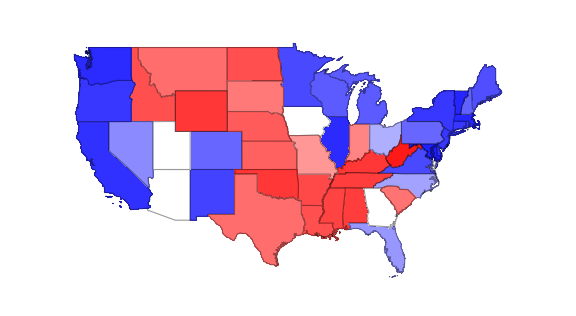
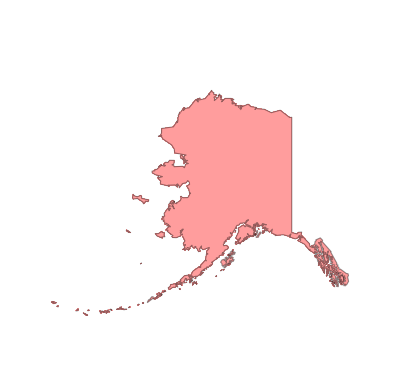
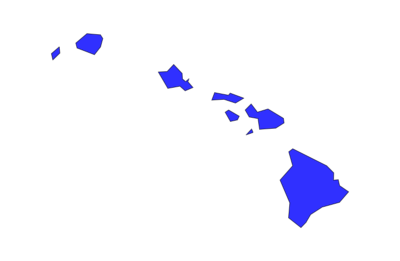
-Graphics-October 12, 2016 08:43 EST |  | 
-Graphics- | -Graphics- | GOP | 158
DEM | 341
UnDec | 39
DEM.PREZPRTY16 | 0.83
REP.PREZPRTY16 | 0.19
OTH.PREZPRTY16 | 0.01 |  | Source: PredictIt.org

```mathematica
ElectoralMap[data_,imageSize_:Medium,threshold_:0.6]:=Module[{},
Return[GeoRegionValuePlot[data,
ColorFunction->(Blend[{{0,Lighter[Blue,0.1]},{1-threshold,White},{threshold,White},{1,Lighter[Red,0.1]}},#1]&),
GeoBackground->None,
GeoProjection-> "Mercator",
PlotLegends->None,
ImageSize->imageSize]]
];

alaska=ElectoralMap[Select[gopByState,MemberQ[{"Alaska"},#⟦1,2,1⟧]&],Tiny,cutoffPercentage];

hawaii=ElectoralMap[Select[gopByState,MemberQ[{"Hawaii"},#⟦1,2,1⟧]&],
Tiny,cutoffPercentage];

lowerFortyEight=Labeled[ElectoralMap[Select[gopByState,!MemberQ[{"Alaska","Hawaii"},#⟦1,2,1⟧]&],
Large,cutoffPercentage],
Style[DateString[timeStamp,{"MonthName"," ","Day",", ","Year"," ","Hour",":","Minute"," ","EST"}],"Subtitle"],Top];

mapOutput=Labeled[Pane[Grid[{{lowerFortyEight,SpanFromLeft},{alaska,hawaii,voteTable},{winningPartyTable}}]],
Style["Source: PredictIt.org","Subsubtitle"]]
```

The last step is to create a dynamic version using Manipulate which allows the user to select a threshold value.

```mathematica
Manipulate[
gopVotes=Total[Select[gopByState,#⟦2⟧≥x&]⟦All,1⟧/.mappedStateVotes];
demVotes=Total[Select[gopByState,#⟦2⟧≤ (1-x)&]⟦All,1⟧/.mappedStateVotes];
undecVotes=Total[Select[gopByState,(1-x)<#⟦2⟧<x&]⟦All,1⟧/.mappedStateVotes];
voteTable=Style[TableForm[{{"GOP",gopVotes},{"DEM",demVotes},{"UnDec",undecVotes},{"Total",Total[{gopVotes,demVotes,undecVotes}]}}],
FontFamily->"Verdana"];

alaska=ElectoralMap[Select[gopByState,MemberQ[{"Alaska"},#⟦1,2,1⟧]&],Tiny,x];

hawaii=ElectoralMap[Select[gopByState,MemberQ[{"Hawaii"},#⟦1,2,1⟧]&],
Tiny,x];

lowerFortyEight=Labeled[ElectoralMap[Select[gopByState,!MemberQ[{"Alaska","Hawaii"},#⟦1,2,1⟧]&],
Large,x],
Style[DateString[timeStamp,{"MonthName"," ","Day",", ","Year"," ","Hour",":","Minute"," ","EST"}],"Subtitle"],Top];

Labeled[Pane[Grid[{{lowerFortyEight,SpanFromLeft},{alaska,hawaii,voteTable}}]],
Style["Data source: PredictIt.org","Subsubtitle"]],
{{x,0.5,"Threshold"},0.50,1,.01,Appearance->"Labeled"},
ContinuousAction->False,
SaveDefinitions->True
]
```

```mathematica
Export["PredictIt Electoral Map "<>DateString[timeStamp,{"Year","Month","Day","Hour","Minute"}]<>".png",mapOutput]
```

PredictIt Electoral Map 201610092246.png

```mathematica
previousMapOutput=Import["PredictIt Electoral Map 201610092102.png"];
```

```mathematica
secondMapOutput=Import["PredictIt Electoral Map 201610092246.png"];
```

```mathematica
Export["PredictIt Electoral Map.gif",{previousMapOutput,secondMapOutput},"GIF","DisplayDurations"->2,"Interlaced"->True]
```

PredictIt Electoral Map.gif